# Zika vaccine MS results

```mathematica
Quit[]
```

## Setup

### Headers

```mathematica
If[$CommandLine[[2]]=="-wstp",ClusterRun=False,ClusterRun=True];
```

```mathematica
If[ClusterRun,SetDirectory["./"],SetDirectory[NotebookDirectory[]]];
```

```mathematica
Import["Zika vaccine model setup.m"]
```

## Figure 1 - Plot time series

### Setup

#### Read in data

```mathematica
SetDirectory[NotebookDirectory[]<>"/GeneratedResults/VaccineImpactTimeSeries"]
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\VaccineImpactTimeSeries

```mathematica
vaccineTimeSeriesScenarios=Get["vaccineTimeSeriesScenarios.dat"];
```

#### Setup plots

```mathematica
Clear@plotFigure1
plotFigure1[data_,outcome_,legend_,cumulative_:False,yrange_:All,ysteps_:Automatic,xrange_:{0,3*52}]:=ListLinePlot[If[cumulative,#[outcome],Differences[#[outcome]]]&/@Values[data],
PlotRange->{xrange,yrange},PlotLegends->legend,
PlotStyle->{Directive[Black,Dashed],Black,Directive[Black,Dotted],Directive[Black,DotDashed],Directive[Black,Dashing]},
LabelStyle->Directive[Black,16],

Frame->{True,True,False,False},
FrameStyle->Black,
FrameLabel->{"Year","Infections"},
FrameTicks->{{If[ysteps==Automatic,Automatic,Range[yrange[[1]],yrange[[2]],ysteps]],None},{{#,#/52}&/@Range[52,52*3,52],None}},

ImageSize->{Automatic,200}
]
```

### Plot “best fit”

#### Plot all infections

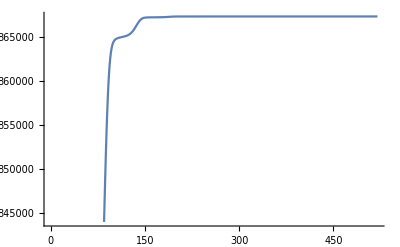

```mathematica
ListLinePlot@vaccineTimeSeriesScenarios["NoVaccination"]["allInfections"]
```

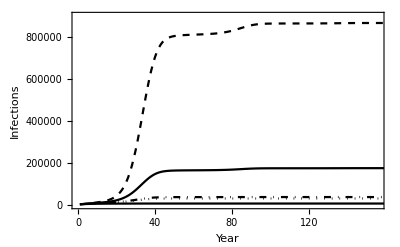

```mathematica
plotFigure1[vaccineTimeSeriesScenarios,"allInfections",None,True,{0,900000},300000]
```

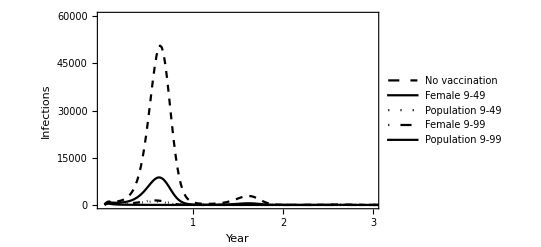

```mathematica
plotFigure1[vaccineTimeSeriesScenarios,"allInfections",{"No vaccination","Female 9-49","Population 9-49","Female 9-99","Population 9-99"},False,{0,60000},20000]
```

#### Plot prenatal infections infections

```mathematica
Keys@vaccineTimeSeriesScenarios
```

{NoVaccination,WHOfemale,WHOall,allfemale,allpopulation}

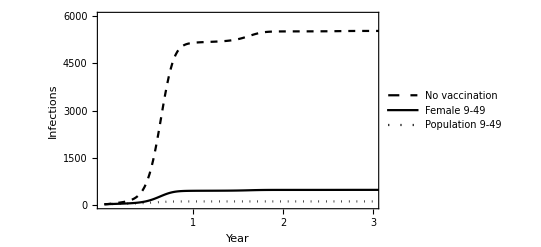

```mathematica
Show[
plotFigure1[vaccineTimeSeriesScenarios[[;;3]],"prenatalInfections",{"No vaccination","Female 9-49","Population 9-49","Female 9-99","Population 9-99"}[[;;3]],True,{0,6000},2000],
Graphics[Text[Style["A",Bold,16],{-10,100}]]
]
```

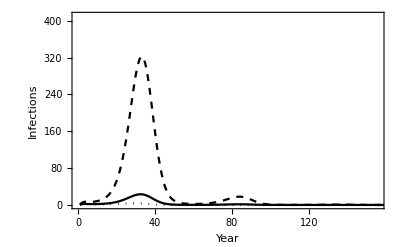

```mathematica
plotFigure1[vaccineTimeSeriesScenarios[[;;3]],"prenatalInfections",None,False,{0,410},100]
```

## Figure 2 - Plot increasing coverage

### Extract the 1000 parameter sets that best fit the predicted attack rate

#### Read in uncertainty data

```mathematica
SetDirectory["C:\\Users\\carbon\\Downloads\\Zika vaccine\\Uncertainty"]
```

C:\Users\carbon\Downloads\Zika vaccine\Uncertainty

Read in all sampled runs

```mathematica
Dynamic@file
```

```mathematica
uncertaintyData=Get/@FileNames[];
```

Read in MLE results

```mathematica
SetDirectory[NotebookDirectory[]<>"\\GeneratedResults\\Uncertainty"]
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\Uncertainty

```mathematica
mleUncertainty=Get["mleUncertaintyDesktop.dat"];
```

#### Choose those with the best least-squares fit to the target MLE

```mathematica
targetSize=1000;
```

```mathematica
MLEprenatalInfections=mleUncertainty["Best fit"]["VaccinateWomen"][0.]["AllPrenatalInfections"]
```

5529.94

```mathematica
Length@uncertaintyData
```

5000

```mathematica
bestfitTable=Table[{i,
(
(uncertaintyData[[i]]["Best fit"]["VaccinateWomen"][0.]["AllPrenatalInfections"]-MLEprenatalInfections)^2
)
},{i,Length@uncertaintyData}];
```

```mathematica
targetIndices=SortBy[bestfitTable,Last][[;;targetSize,1]];
```

### Generate 95% CI plot

#### Setup function

```mathematica
Keys[uncertaintyData[[1]]["Best fit"]["VaccinateWomen"]]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95}

```mathematica
Clear@plotVaccineUncertainty
plotVaccineUncertainty[data_,leftLabel_:True]:=ListLinePlot[data,

DataRange->{0,90},PlotRange->{{0,90},{0,9000}},

Frame->{True,True,False,False},FrameStyle->Black,FrameTicks->{{{#,#/1000}&/@Range[0,9000,3000],None},{Range[0,90,30],None}},
FrameLabel->{{If[leftLabel,"Prenatal infections
(thousands)",""],None},{"Coverage",None}},

LabelStyle->18,
ImageSize->350,

PlotStyle->{Directive[Black,Dotted],Black,Directive[Black,Dotted]}
]
```

#### Plot absolute # of cases with CIs

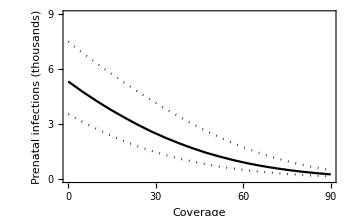

```mathematica
plotVaccineUncertainty[Transpose[
(Sort[#][[{1,500,1000}]])&/@Transpose[Table[((unc["Best fit"]["VaccinateWomen"][#]["AllPrenatalInfections"]&/@Keys[unc["Best fit"]["VaccinateWomen"]])),{unc,uncertaintyData[[targetIndices]]}]]],True]
```

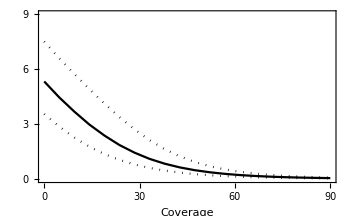

```mathematica
plotVaccineUncertainty[Transpose[
(Sort[#][[{1,500,1000}]])&/@Transpose[Table[((unc["Best fit"]["VaccinateMenAndWomen"][#]["AllPrenatalInfections"]&/@Keys[unc["Best fit"]["VaccinateWomen"]])),{unc,uncertaintyData[[targetIndices]]}]]],False]
```

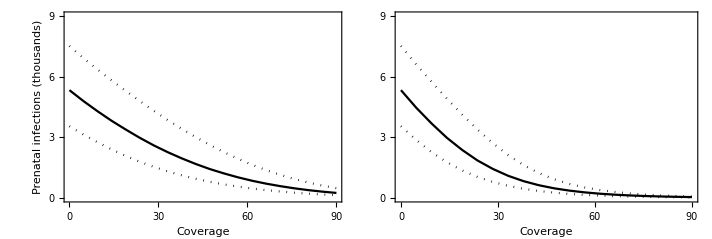

```mathematica
Show[
GraphicsRow[{
plotVaccineUncertainty[Transpose[
(Sort[#][[{1,500,1000}]])&/@Transpose[Table[((unc["Best fit"]["VaccinateWomen"][#]["AllPrenatalInfections"]&/@Keys[unc["Best fit"]["VaccinateWomen"]])),{unc,uncertaintyData[[targetIndices]]}]]],True],
plotVaccineUncertainty[Transpose[
(Sort[#][[{1,500,1000}]])&/@Transpose[Table[((unc["Best fit"]["VaccinateMenAndWomen"][#]["AllPrenatalInfections"]&/@Keys[unc["Best fit"]["VaccinateWomen"]])),{unc,uncertaintyData[[targetIndices]]}]]],False]
},0],
Graphics[Text[Style["A",Bold,16],{45,-16}]],
Graphics[Text[Style["B",Bold,16],{370,-16}]]
]
```

## Table 1 - Generate table of outcomes

Data tables are assumed to have already been defined under “Figure 2 / Extract 1000” section above

### Generate the table

#### Setup functions

```mathematica
Clear@pullTableRow
pullTableRow[data_,target_,vscen_,outcome_,ageoutcome_,maleoutcome_:""]:=Join[
{data[target][vscen][outcome]+If[maleoutcome=="",0,data[target][vscen][maleoutcome]],
If[maleoutcome=="","",data[target][vscen][maleoutcome]],
data[target][vscen][outcome]},
Values[data[target][vscen][ageoutcome]]]
```

```mathematica
Clear@pregnancyRow
pregnancyRow[data_,target_]:=pullTableRow[data,target,0.,"AllPregnancies","PregnanciesAgeGroup"]
```

```mathematica
Clear@prenatalInfRow
prenatalInfRow[data_,target_,covg_]:=pullTableRow[data,target,covg,"AllPrenatalInfections","PrenatalInfectionsAgeGroup"]
```

```mathematica
Clear@vaccRow
vaccRow[data_,target_,covg_]:=pullTableRow[data,target,covg,"FemaleVaccines","FemaleVaccinesAgeGroup","MaleVaccines"]
```

pullOutcome[func_, round_: 1] extracts the MLE and min/max parameter sample results
func is a function that accepts the solution as input

```mathematica
Clear@pullOutcome
pullOutcome[func_,range_:True,(*round_:1,*)percentage_:False]:=With[{
mleData=func[mleUncertainty["Best fit"]],
ciRange=Table[func[unc["Best fit"]],{unc,uncertaintyData[[targetIndices]]}]
(*ciRange=func/@uncertaintyData[[targetIndices]]*)
},
Table[
If[mleData[[i]]=="","",
If[range,
(
ToString[Round[mleData[[i]]*If[percentage,100,1]]]<>If[percentage,"%",""]<>" ("<>ToString[Round[Min[ciRange[[All,i]]]*If[percentage,100,1]]]<>"-"<>ToString[Round[Max[ciRange[[All,i]]]*If[percentage,100,1]]]<>If[percentage,"%",""]<>")"
),
(
ToString[Round[mleData[[i]]*If[percentage,100,1]]]<>If[percentage,"%",""]
)]
(*(
ToString[Round[mleData[[i]],round]]<>" ("<>ToString[Round[Min[ciRange[[All,i]]],round]]<>"-"<>ToString[Round[Max[ciRange[[All,i]]],round]]<>")"
)*)],{i,Length[mleData]}]]
```

```mathematica
pullOutcome[pregnancyRow[#,"VaccinateWomen"]&,False]//MatrixForm
```

(29226

29226
733
3605
7865
8545
5818
2223
419
18)

#### Create the table

```mathematica
Join[{{"","","No vaccination","","Vaccinate 50% of females 9-49","","","Vaccinate 50% of population 9-49","","","Vaccinate 90% of females 9-49","","","Vaccinate 90% of population 9-49",""},{"Age","Pregnancies","Prenatal infections","Prenatal infections","Reduction","Vaccines","Prenatal infections","Reduction","Vaccines","Prenatal infections","Reduction","Vaccines","Prenatal infections","Reduction","Vaccines"}},
Transpose[Join[{{"Population","Men","Women","9-14","15-19","20-24","25-29","30-34","35-39","40-44","45-49"}},{
pullOutcome[pregnancyRow[#,"VaccinateWomen"]&,False],
pullOutcome[prenatalInfRow[#,"VaccinateWomen",0.]&],

pullOutcome[prenatalInfRow[#,"VaccinateWomen",0.5]&],
pullOutcome[(1-prenatalInfRow[#,"VaccinateWomen",0.5]/prenatalInfRow[#,"VaccinateWomen",0.])&,True,True(*0.01*)],
pullOutcome[vaccRow[#,"VaccinateWomen",0.5]&,False],

pullOutcome[prenatalInfRow[#,"VaccinateMenAndWomen",0.5]&],
pullOutcome[(1-prenatalInfRow[#,"VaccinateMenAndWomen",0.5]/prenatalInfRow[#,"VaccinateMenAndWomen",0.])&,True,True(*0.01*)],
pullOutcome[vaccRow[#,"VaccinateMenAndWomen",0.5]&,False],

pullOutcome[prenatalInfRow[#,"VaccinateWomen",0.9]&],
pullOutcome[(1-prenatalInfRow[#,"VaccinateWomen",0.9]/prenatalInfRow[#,"VaccinateWomen",0.])&,True,True(*0.01*)],
pullOutcome[vaccRow[#,"VaccinateWomen",0.9]&,False],

pullOutcome[prenatalInfRow[#,"VaccinateMenAndWomen",0.9]&],
pullOutcome[(1-prenatalInfRow[#,"VaccinateMenAndWomen",0.9]/prenatalInfRow[#,"VaccinateMenAndWomen",0.])&,True,True(*0.01*)],
pullOutcome[vaccRow[#,"VaccinateMenAndWomen",0.9]&,False]
}]]
]//MatrixForm
```

( |  | No vaccination |  | Vaccinate 50% of females 9-49 |  |  | Vaccinate 50% of population 9-49 |  |  | Vaccinate 90% of females 9-49 |  |  | Vaccinate 90% of population 9-49 | 
Age | Pregnancies | Prenatal infections | Prenatal infections | Reduction | Vaccines | Prenatal infections | Reduction | Vaccines | Prenatal infections | Reduction | Vaccines | Prenatal infections | Reduction | Vaccines
Population | 29226 | 5530 (3551-7503) | 1538 (812-2625) | 72% (65-78%) | 640383 | 540 (278-939) | 90% (87-93%) | 1274553 | 358 (188-626) | 94% (92-95%) | 1149986 | 76 (52-111) | 99% (98-99%) | 2277208
Men |  |  |  | 0% (0-0%) | 0 |  | 0% (0-0%) | 636765 |  | 0% (0-0%) | 0 |  | 0% (0-0%) | 1137387
Women | 29226 | 5530 (3551-7503) | 1538 (812-2625) | 72% (65-78%) | 640383 | 540 (278-939) | 90% (87-93%) | 637788 | 358 (188-626) | 94% (92-95%) | 1149986 | 76 (52-111) | 99% (98-99%) | 1139821
9-14 | 733 | 140 (89-190) | 39 (20-66) | 72% (65-78%) | 176883 | 14 (7-24) | 90% (87-93%) | 174288 | 9 (5-16) | 94% (92-95%) | 315686 | 2 (1-3) | 99% (98-99%) | 305520
15-19 | 3605 | 767 (491-1042) | 213 (113-363) | 72% (65-78%) | 66500 | 75 (39-130) | 90% (87-93%) | 66500 | 50 (26-87) | 94% (92-95%) | 119700 | 11 (7-15) | 99% (98-99%) | 119700
20-24 | 7865 | 1643 (1062-2248) | 457 (243-785) | 72% (65-78%) | 70000 | 160 (83-280) | 90% (87-93%) | 70000 | 107 (56-188) | 94% (92-95%) | 126000 | 23 (15-33) | 99% (98-99%) | 126000
25-29 | 8545 | 1505 (964-2039) | 419 (220-715) | 72% (65-78%) | 66000 | 147 (75-255) | 90% (87-93%) | 66000 | 97 (51-170) | 94% (92-95%) | 118800 | 21 (14-30) | 99% (98-99%) | 118800
30-34 | 5818 | 996 (636-1350) | 277 (146-470) | 72% (65-78%) | 66000 | 97 (50-169) | 90% (87-93%) | 66000 | 64 (34-112) | 94% (92-95%) | 118800 | 14 (9-20) | 99% (98-99%) | 118800
35-39 | 2223 | 403 (256-546) | 112 (59-190) | 72% (65-78%) | 66500 | 39 (20-68) | 90% (87-93%) | 66500 | 26 (14-45) | 94% (92-95%) | 119700 | 6 (4-8) | 99% (98-99%) | 119700
40-44 | 419 | 74 (47-100) | 20 (11-35) | 72% (65-78%) | 64500 | 7 (4-12) | 90% (87-93%) | 64500 | 5 (2-8) | 94% (92-95%) | 116100 | 1 (1-1) | 99% (98-99%) | 116100
45-49 | 18 | 3 (2-4) | 1 (0-1) | 72% (65-78%) | 64000 | 0 (0-1) | 90% (87-93%) | 64000 | 0 (0-0) | 94% (92-95%) | 115200 | 0 (0-0) | 99% (98-99%) | 115200)

## Figure 3 - Plot contour scenarios

### Setup

#### Read in results

```mathematica
SetDirectory[NotebookDirectory[]<>"GeneratedResults/PriorRcontours"]
contourResults=Association[(#->Get["results_"<>#<>".dat"])&/@{"Puerto Rico"}(*CountryNames*)];
SetDirectory[NotebookDirectory[]];
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\PriorRcontours

```mathematica
skipFunc=Function[data,data["attR"]==0.35||data["attR"]>0.5]
```

Function[data,data[attR]==0.35||data[attR]>0.5]

```mathematica
MinMax[#["attR"]&/@contourResults["Puerto Rico"]]
```

{0.05,0.55}

```mathematica
attRRange=Sort@DeleteDuplicates[#["attR"]&/@contourResults["Puerto Rico"]]
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55}

```mathematica
vrateRange=Sort@DeleteDuplicates[#["vrate"]&/@contourResults["Puerto Rico"]]
```

{0,0.5,0.9}

```mathematica
priorRRange=Sort@DeleteDuplicates[#["priorR"]&/@contourResults["Puerto Rico"]]
```

{0.,0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95}

#### Add in 0 attack rate data for contour plotting

```mathematica
contourResults["Puerto Rico"]=Join[contourResults["Puerto Rico"],Flatten[Table[Association[{"attR"->attR,"vrate"->vrate,"priorR"->priorR,
"Results"->
With[{dummyResult=First[Select[contourResults["Puerto Rico"],(#["vrate"]==vrate&&#["priorR"]==priorR)&]]["Results"]},
Association[{"vaccines"->dummyResult["vaccines"],"prenatalInfections"->0.1,"pregnancies"->dummyResult["pregnancies"],"population"->dummyResult["population"]}]
]
}
],{attR,{0}},{vrate,vrateRange},{priorR,priorRRange}]]];
```

#### Define functions

```mathematica
Clear[extractContour]
extractContour[data_,contourIn_]:=With[{toret=Flatten[Cases[Normal@ListContourPlot[data,Contours->{contourIn},PlotRange->{0,Max[data]}],Tooltip[contour_,label_]:>Cases[contour,l_Line:>ArrayPad[First@l,{{0},{0,1}},label]],Infinity],1]},
If[toret=={},{},toret[[1,All,{1,2}]]]]
```

```mathematica
Clear@plotAttrContour
plotAttrContour[country_,vrate_,contours_,colorscheme_,maxCont_:0,minContour_:0.5,labelsize_:16,contourlabelsize_:12,plotlabel_:"",xlabel_:"",ylabel_:"",xrange_:{0,0.5},yrange_:{0,0.5}]:=
With[{data={#["attR"],#["priorR"],1000*#["Results"]["prenatalInfections"]/#["Results"]["pregnancies"]}&/@Select[contourResults[country],(#["vrate"]==vrate&&!skipFunc[#])&]},
With[{
maxContour=If[maxCont==0,Floor[Max[Flatten[data[[All,3]]]]*1.2],maxCont]
},
Show[

ListLinePlot[
Sow[(With[{calldata=extractContour[data,#]},
If[calldata=={},Nothing,

Callout[calldata,
Style[ToString[#],12],
Automatic,
MaximalBy[extractContour[data,#],First],
LeaderSize->{2,0°,5}]
(*Callout[calldata,Style[ToString[#],contourlabelsize]]*)

]]&/@contours)],PlotStyle->None,AspectRatio->1,PlotRange->{xrange,yrange},
PlotRangeClipping->False,ImagePadding->{{40,50},{20,20}},

##],

ListContourPlot[data,
Contours->contours,ContourStyle->None,ColorFunctionScaling->False,
ColorFunction->(ColorData[colorscheme][((Log[#]-Log[minContour])/(Log[maxContour]-Log[minContour]))]&),
ClippingStyle->Automatic,PlotRange->{xrange,yrange,All},
RegionFunction->Function[{x,y,z},xrange[[1]]≤x≤xrange[[2]]&&yrange[[1]]≤y≤yrange[[2]]],

##],

PlotRange->{xrange,yrange}

]&[
PlotLabel->plotlabel,

Frame->{True,True,False,False},FrameStyle->Black,FrameLabel->{xlabel,ylabel},
FrameTicks->{{{#,ToString[Floor[100*#]]<>"%"}&/@{yrange[[1]],Mean@yrange,yrange[[2]]},None},{{#,ToString[Floor[100*#]]<>"%"}&/@{xrange[[1]],Mean@xrange,xrange[[2]]},None}},

ImageSize->250,

LabelStyle->Directive[Black,labelsize],
ImagePadding->{{60,40},{60,0}}
]
]
]
```

```mathematica
(*Clear[barLegend]
barLegend[maxContour_,colorscheme_,labelsize_,minContour_,contourlabelsteps_]:=BarLegend[{(ColorData[colorscheme][1-#(*(Log[#]-Log[0.1])/(Log[1000]-Log[0.1])*)]&),{0,1}},LegendLabel->" Zika infections per
  1000 pregnancies",LabelStyle->Directive[Black,Alignment->Center,labelsize],Ticks->With[{tickReplace=({#,If[#≥1.0,Round[#],#]&[Exp[#*(Log[(*1000*)maxContour]-Log[minContour])+Log[minContour]]]}&/@contourlabelsteps)},Transpose[{tickReplace[[All,1]],Reverse[tickReplace[[All,2]]]}]]]*)
```

```mathematica
Clear[barLegend]
barLegend[maxContour_,colorscheme_,labelsize_,contourlabelsteps_]:=BarLegend[colorscheme,LegendLabel->" Zika infections per
  1000 pregnancies",LabelStyle->Directive[Black,Alignment->Center,labelsize],
"Ticks"->Range[0,1,1/(contourlabelsteps-1)],
"TickLabels"->(ToString[N@((maxContour/1000)*10^(3*(1-#)))]&/@Range[0,1,1/(contourlabelsteps-1)])]
```

```mathematica
barLegend[400,"CherryTones",16,4]
```

```mathematica
MasterPlotFigure2["Puerto Rico",False,{5,10,25,100,200,300},300,0.5]
```

-Graphics-

```mathematica
Clear[MasterPlotFigure2]
MasterPlotFigure2[country_,label_:True,contours_:{5,10,25,100,200,400},
maxCont_:500,minContour_:0.5]:=With[{colorscheme="CherryTones",labelsize=16,contourlabelsize=12,xlabel="Attack rate",ylabel="Existing immunity",
contourlabelsteps=4(*Range[0,1,1/3]*)},

Labeled[
Show[
Legended[
GraphicsRow[
{
plotAttrContour[country,0,contours,{colorscheme,"Reverse"},maxCont,minContour,labelsize,contourlabelsize,"No vaccination","",ylabel],
plotAttrContour[country,0.5,contours,{colorscheme,"Reverse"},maxCont,minContour,labelsize,contourlabelsize,"50% coverage",xlabel,""],
plotAttrContour[country,0.9,contours,{colorscheme,"Reverse"},maxCont,minContour,labelsize,contourlabelsize,"90% coverage","",""]
}
],

barLegend[maxCont,colorscheme,labelsize,contourlabelsteps]],
Graphics[Text[Style["A",Bold,labelsize],{30,-31}]],
Graphics[Text[Style["B",Bold,labelsize],{290,-31}]],
Graphics[Text[Style["C",Bold,labelsize],{560,-31}]]
],
If[label,Text[Style[country,Bold,labelsize]],""],Top]
]
```

### Plots

#### Plot Puerto Rico

### Extract specific results

#### 25% attack rate

```mathematica
Table[
vrate->With[{res=
Select[contourResults["Puerto Rico"],(
#["attR"]==0.25&&#["vrate"]==vrate&&#["priorR"]==0.25
)&][[1]]["Results"]},
res["prenatalInfections"]/res["pregnancies"]*1000],
{vrate,{0.5,0.9}}
]
```

{0.5→5.19872,0.9→2.05964}

```mathematica
With[{res=
Select[contourResults["Puerto Rico"],(
#["attR"]==0.25&&#["vrate"]==0&&#["priorR"]==0.
)&][[1]]["Results"]},
res["prenatalInfections"]/res["pregnancies"]*1000]
```

192.416

## Figure 4 - Plot age-specific targeting vs fertility

### Read in data

```mathematica
SetDirectory[NotebookDirectory[]<>"/GeneratedResults/AgeScenarios"]
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\AgeScenarios

Indirect protection

```mathematica
indirect=Association[Table[country->
Association[Table[attR->
Association[Table[lag->Get["indirectProtectionLow_"<>country<>"_attR_"<>ToString@attR<>"_lag_"<>ToString@lag<>".dat"],{lag,{0(*,10*)}}]],{attR,{0.25(*,0.5*)}}]],{country,CountryNames}]];
```

No vaccine results

```mathematica
noVaccine=Association[Table[country->
Association[Table[attR->
Association[Table[lag->Get["noVaccineResult_"<>country<>"_attR_"<>ToString@attR<>"_lag_"<>ToString@lag<>".dat"],{lag,{0(*,10*)}}]],{attR,{0.25(*,0.5*)}}]],{country,CountryNames}]];
```

Results frontier (age-specific coverage)

```mathematica
results5yr=Association[Table[country->
Association[Table[attR->
Association[Table[lag->Get["vaccResults5yr_"<>country<>"_attR_"<>ToString@attR<>"_lag_"<>ToString@lag<>".dat"],{lag,{0(*,10*)}}]],{attR,{0.25(*,0.5*)}}]],{country,CountryNames}]];
```

Male targeted results

```mathematica
targetMen=Association[Table[country->
Association[Table[attR->
Association[Table[lag->Get["targetMenLow_"<>country<>"_attR_"<>ToString@attR<>"_lag_"<>ToString@lag<>".dat"],{lag,{0(*,10*)}}]],{attR,{0.25(*,0.5*)}}]],{country,CountryNames}]];
```

#### Quick-access functions

```mathematica
Clear@pullIndirectData
pullIndirectData[country_,attR_,lag_]:=indirect[country][attR][lag]
```

```mathematica
pullIndirectData["Puerto Rico",0.25,0]
```

<|vaccines→27580.,prenatalInfections→5685.4,pregnancies→29226.1,population→3.75206×10^6|>

```mathematica
Clear@pullMaleData
pullMaleData[country_,attR_,lag_]:=targetMen[country][attR][lag]
```

```mathematica
pullMaleData["Puerto Rico",0.25,0]
```

<|vaccines→510.,prenatalInfections→5873.3,pregnancies→29226.1,population→3.75206×10^6|>

```mathematica
Clear@pullNoVaccData
pullNoVaccData[country_,attR_,lag_]:=noVaccine[country][attR][lag]["Results"]
```

```mathematica
pullNoVaccData["Puerto Rico",0.25,0]
```

<|vaccines→0.,prenatalInfections→5876.85,pregnancies→29226.1,population→3.75206×10^6|>

```mathematica
Clear@pull5yrData
pull5yrData[country_,attR_,lag_,lowAge_,highAge_,mvacc_]:=Select[(results5yr[country][attR][lag]),#["LowAge"]==lowAge&&#["HighAge"]==highAge&&#["MaleVaccination"]==mvacc&][[1]]["Results"]
```

```mathematica
pull5yrData["Puerto Rico",0.25,0,10,14,False]
```

<|vaccines→1170.,prenatalInfections→5867.58,pregnancies→29226.1,population→3.75206×10^6|>

### Plot

#### Setup plotting function

```mathematica
Clear@plotAgeTargetingFertilityNonSexual
plotAgeTargetingFertilityNonSexual[country_,attR_,yrange_,fertilityScaling_,{leftLabel_:True,rightLabel_:True,bottomLabel_:True,plotlabel_:False}]:=
With[{
dataToPlot=((pullNoVaccData[country,attR,0]["prenatalInfections"]-pull5yrData[country,attR,0,#,#+4,False]["prenatalInfections"])/pull5yrData[country,attR,0,#,#+4,False]["vaccines"])&/@Range[10,45,5],
indirect=(pullNoVaccData[country,attR,0]["prenatalInfections"]-pullIndirectData[country,attR,0]["prenatalInfections"])/pullIndirectData[country,attR,0]["vaccines"],
fert=Prepend[birthRateByCountry[country][[;;7]],youngerBirthRate[country]]
},
With[{
fertility=fert*(Ceiling[Max[dataToPlot],0.02]/Max[fert])/fertilityScaling
},
ListLinePlot[
{
fertility,
{{1,#},{8,#}}&[indirect],
dataToPlot
},

(*Define the plot lines*)
PlotStyle->{Directive[Black,Thin,Dotted],Directive[Black,Thin,Dashed],Directive[Black,Thin]},

(*Plot a range extending to the nearest 20 cases per 1k vaccines*)
PlotRange->{{0.5,8.5},{0,Ceiling[Max[dataToPlot],0.02]}},

LabelStyle->Directive[Black,16],

PlotLabel->If[plotlabel,country,None],
ImageSize->400,

(*Define the frame*)
Frame->{True,True,False,True},FrameStyle->Black,
FrameTicks->{
{
({#,1000*#}&/@Range[0,0.1,0.02]),
{#,1000*#*Max[fert]*fertilityScaling/Ceiling[Max[dataToPlot],0.02]}&/@Range[0,Max[fertility],Max[fertility]/4]*fertilityScaling
},
{
{{1,Rotate["10-14", 45 Degree]},{2,Rotate["15-19", 45 Degree]},{3,Rotate["20-24", 45 Degree]},{4,Rotate["25-29", 45 Degree]},{5,Rotate["30-34", 45 Degree]},{6,Rotate["35-39", 45 Degree]},{7,Rotate["40-44", 45 Degree]},{8,Rotate["45-49", 45 Degree]}},
None}},
FrameLabel->{If[bottomLabel,"Age group vaccinated",""],If[leftLabel,"Infection averted
per 1000 vaccines",""],None,If[rightLabel,Rotate["Fertility per 1000 women",Pi],""]}
]
]
]
```

```mathematica
maxFertility=Association[(#->(Max@fullFertility@#))&/@{"Puerto Rico","Costa Rica","Dominica","Brazil"}]
```

<|Puerto Rico→0.0959,Costa Rica→0.1011,Dominica→0.1165,Brazil→0.1076|>

```mathematica
maxRound2pct=Association[(#->Ceiling[maxFertility@#,0.02])&/@{"Puerto Rico","Costa Rica","Dominica","Brazil"}]
```

<|Puerto Rico→0.1,Costa Rica→0.12,Dominica→0.12,Brazil→0.12|>

```mathematica
Clear@featurePlot
featurePlot[country_,left_,right_,bottom_]:=With[{fertilityScaling=2*maxRound2pct[country]/maxFertility[country]},plotAgeTargetingFertilityNonSexual[country,0.25,0,fertilityScaling,{left,right,bottom,True}]]
```

#### Generate Figure 4

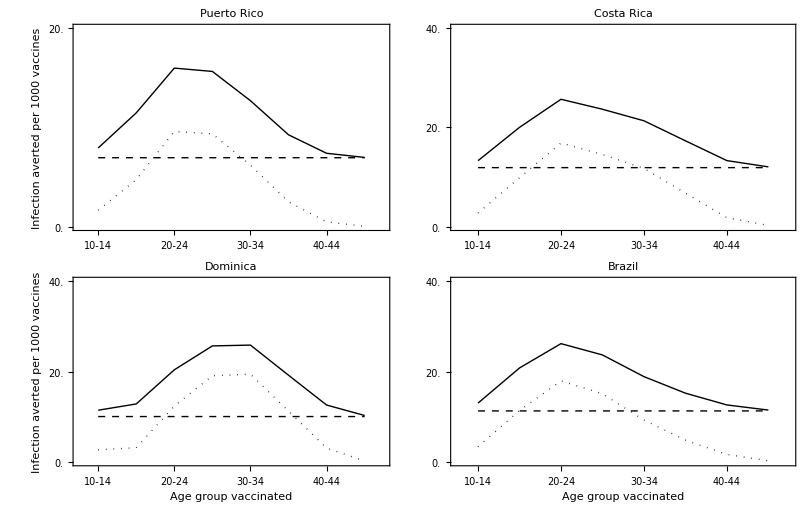

```mathematica
GraphicsGrid[{
{featurePlot["Puerto Rico",True,False,False],featurePlot["Costa Rica",False,True,False]},
{featurePlot["Dominica",True,False,True],featurePlot["Brazil",False,True,True]}
},Spacings->0]
```

## Figure 5 - Plot frontier

### Compute best fit hull/frontier for Puerto Rico

#### Read in results

No vaccine scenario

```mathematica
SetDirectory[NotebookDirectory[]<>"/GeneratedResults/AgeScenarios/"]
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\AgeScenarios

```mathematica
noVaccineResult=Get["noVaccineResult_Puerto Rico_attR_0.25_lag_0.dat"];
```

Core scenarios

```mathematica
vaccResultsFrontier=Get["resultsFrontier_Puerto Rico_attR_0.25_lag_0.dat"];
```

#### Setup results data

```mathematica
Clear@computedResultsFunction
computedResultsFunction[noVaccineResult_,vaccResultsFrontier_]:=Table[{(noVaccineResult["Results"]["prenatalInfections"]-vacc["Results"]["prenatalInfections"]),vacc["Results"]["vaccines"],ToString["LowAge"/.vacc]<>" to "<>ToString["HighAge"/.vacc]<>If["MaleVaccination"/.vacc," All"," Women"]},{vacc,vaccResultsFrontier}];
```

#### Extract convex hull

```mathematica
iterateHullSelection[{minVaccScen_,computedResultsSubset_}]:=
With[{minchoice=MinimalBy[

Append[#,((#[[2]]-minVaccScen[[1,2]])/(#[[1]]-minVaccScen[[1,1]]))]&/@Select[computedResultsSubset,#[[1]]>minVaccScen[[1,1]]&],

Last]},
{minchoice,Complement[computedResultsSubset,minchoice[[;;,;;3]]]}]
```

computeConvexHull returns the set of scenarios that are optimal, eg for which no other scenario produces more benefit for the same or lower cost

```mathematica
Clear@computeConvexHull
computeConvexHull[computedResults_]:=
With[{
(*First, compute the scenario with fewest number of vaccines administered*)
minVaccScen=MinimalBy[computedResults,Second]
},
With[{
(*Second, extract the subset of the results excluding minVaccScen*)
computedResultsSubset=Complement[computedResults,minVaccScen]},

(*Remove empty results {} that are returned once the loop finishes*)
DeleteCases[
(*Recursively call iterateHullSelection for the length of the dataset*)
NestList[iterateHullSelection,{minVaccScen,computedResultsSubset},Length[computedResultsSubset]][[All,1]],{}][[All,1,;;3]]]]
```

#### Plot

```mathematica
computedResults=computedResultsFunction[noVaccineResult,vaccResultsFrontier];
```

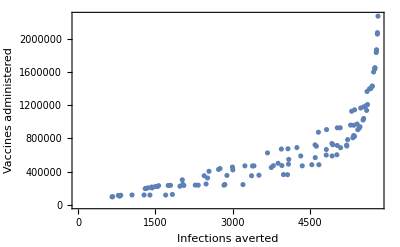

```mathematica
ListPlot[Tooltip[#[[;;2]],#[[3]]]&/@computedResults,Frame->{True,True,False,False},FrameLabel->{"Infections averted","Vaccines administered"}]
```

#### Compute convex hull

Compute the scenario with fewest number of vaccines administered

```mathematica
minVaccScen=MinimalBy[computedResults,Second]
```

{{660.657,97200.,0 to 4 Women}}

Extract subset remaining

```mathematica
computedResultsSubset=Complement[computedResults,minVaccScen];
```

```mathematica
minVaccScen[[1]]
```

{660.657,97200.,0 to 4 Women}

```mathematica
MinimalBy[Append[#,((#[[2]]-minVaccScen[[1,2]])/(#[[1]]-minVaccScen[[1,1]]))]&/@computedResultsSubset,Last]
```

{{1700.6,118800.,25 to 29 Women,20.7703}}

```mathematica
data[[1]]
```

{660.657,97200.,F 0-4}

```mathematica
data=computeConvexHull[Prepend[computedResults,{0,0,"Status quo"}](*computedResults*)];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
data={#[[1]],#[[2]],
StringReplace[If[StringContainsQ[#[[3]],"Women"],"F "<>StringReplace[#[[3]]," Women"->""],"M/F "<>StringReplace[#[[3]]," All"->""]]," to "->"-"]}&/@data
```

{{0,0,M/F Status quo},{1831.54,126000.,F 20-24},{3201.27,244800.,F 20-29},{4065.62,363600.,F 20-34},{4674.29,483300.,F 15-34},{5023.58,603000.,F 15-39},{5216.39,708300.,F 10-39},{5365.76,824400.,F 10-44},{5457.54,923400.,F 5-44},{5471.38,939600.,F 10-49},{5531.01,1.0206×10^6,F 0-44},{5543.48,1.0386×10^6,F 5-49},{5600.73,1.1358×10^6,F 0-49},{5711.28,1.4274×10^6,M/F 10-39},{5763.62,1.6488×10^6,M/F 10-44},{5791.68,1.854×10^6,M/F 5-44},{5792.93,1.8648×10^6,M/F 10-49},{5809.17,2.0529×10^6,M/F 0-44},{5810.42,2.07×10^6,M/F 5-49},{5821.39,2.2689×10^6,M/F 0-49}}

```mathematica
leaderLength={{-10400.,0.},{200,-50000},{400,-175000},{350,-175000},{300,-110000},{200,-50000},{-200,-50000},{200,-50000},{-200,-75000},{200,-75000},{-400,0},{-300,150000},{150,0},{200,100000},{0,0},{0,0},{-400.,0.},{0.,0.},{-400,0},{0,0},{0,0}}
```

### Plot frontier with variable labels

```mathematica
With[{len=100,xmin=-40000,ymin=-2500000,xmax=40000,ymax=2500000},
TabView[{
Slider2D[Dynamic@leaderLength[[1]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[2]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[3]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[4]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[5]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[6]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[7]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[8]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[9]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[10]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[11]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[12]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[13]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[14]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[15]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[16]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[17]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[18]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[19]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[20]],{{xmin,ymin},{xmax,ymax}}],
Slider2D[Dynamic@leaderLength[[21]],{{xmin,ymin},{xmax,ymax}}]}]
]
```

123456789101112131415161718192021

Use the 2d slider bars above to adjust the position of each of the 18 labels

```mathematica
leaderLength[[5]]={300,-110000}
```

{300,-110000}

```mathematica
Dynamic@ListPlot[{
computedResults[[All,;;2]],
Table[Callout[
Style[data[[hull,;;2]],If[StringContainsQ[data[[hull,3]],"M/F"],Black,Red]],
StringSplit[data[[hull,3]]," "][[2]],
data[[hull,;;2]]+leaderLength[[hull]]],
{hull,Length@data}]},
Frame->{True,True,False,False},FrameLabel->{"Infections averted","Vaccines administered"},FrameStyle->Black,FrameTicks->{{Range[0,2500000,500000],None},{Range[0,35000,5000],None}},
PlotRange->{{0,10000},{-500000,2500000}},PlotStyle->{GrayLevel[0.75],Black}]
```

```mathematica
leaderLength[[2]]={200,-50000}(*0,-100000*)
```

{200,-50000}

```mathematica
leaderLength[[3]]={400,-175000}(*{500,-250000}*)
```

{400,-175000}

After updating the label positions, re-generate the plot below non-dynamically for export

```mathematica
Legended[
ListPlot[{
computedResults[[All,;;2]],
Table[Callout[
Style[data[[hull,;;2]],If[StringContainsQ[data[[hull,3]],"M/F"],Black,Red]],
StringSplit[data[[hull,3]]," "][[2]],
data[[hull,;;2]]+leaderLength[[hull]]],
{hull,Length@data}]},
Frame->{True,True,False,False},FrameLabel->{"Infections averted","Vaccines administered"},FrameStyle->Black,FrameTicks->{{Range[0,2500000,500000],None},{Range[0,7500,2500],None}},
PlotRange->{{0,7500},{-500000,2500000}},PlotStyle->{GrayLevel[0.75],Black}],
PointLegend[{Red,Black},{"F","M/F"}]]
```

-Graphics-

### Extract hull for all countries

#### Read in results

No vaccine scenario

```mathematica
SetDirectory[NotebookDirectory[]<>"/GeneratedResults/AgeScenarios"]
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\AgeScenarios

```mathematica
noVaccineResult=Association[Table[country-> 
Association[Table[lag->
Get["noVaccineResult_"<>country<>"_attR_0.25_lag_"<>ToString@lag<>".dat"],
{lag,{0,10}}]],
{country,CountryNames}]];
```

Core scenarios

```mathematica
vaccResultsFrontier=Association[Table[country-> 
Association[Table[lag->
Get["resultsFrontier_"<>country<>"_attR_0.25_lag_"<>ToString@lag<>".dat"],
{lag,{0,10}}]],
{country,CountryNames}]];
```

Compute convex hull for all countries

```mathematica
hull=Association[Table[country->
Association[Table[lag->
computeConvexHull[computedResultsFunction[noVaccineResult[country][lag],vaccResultsFrontier[country][lag]]],
{lag,{0,10}}]],
{country,CountryNames}]];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
hull[[All,All,1,;;2]]={0,0}
```

{0,0}

```mathematica
computedResultsFunction[noVaccineResult["Aruba"][10],vaccResultsFrontier["Aruba"][10]]
```

{{25.837,2700.05,0 to 4 Women},{54.161,5400.09,0 to 9 Women},{98.4294,9000.14,0 to 14 Women},{133.842,12600.2,0 to 19 Women},{154.29,16200.2,0 to 24 Women},{161.503,18900.3,0 to 29 Women},{165.072,21600.3,0 to 34 Women},{168.268,25200.4,0 to 39 Women},{170.547,28800.4,0 to 44 Women},{172.18,32400.5,0 to 49 Women},{30.376,2700.05,5 to 9 Women},{80.3855,6300.09,5 to 14 Women},{122.237,9900.14,5 to 19 Women},{147.319,13500.2,5 to 24 Women},{156.457,16200.2,5 to 29 Women},{161.132,18900.3,5 to 34 Women},{165.398,22500.3,5 to 39 Women},{168.455,26100.4,5 to 44 Women},{170.641,29700.4,5 to 49 Women},{56.1291,3600.05,10 to 14 Women},{105.214,7200.09,10 to 19 Women},{136.024,10800.1,10 to 24 Women},{147.852,13500.2,10 to 29 Women},{154.279,16200.2,10 to 34 Women},{160.356,19800.3,10 to 39 Women},{164.77,23400.3,10 to 44 Women},{167.93,27000.4,10 to 49 Women},{61.7296,3600.05,15 to 19 Women},{103.517,7200.09,15 to 24 Women},{121.442,9900.14,15 to 29 Women},{132.565,12600.2,15 to 34 Women},{143.947,16200.2,15 to 39 Women},{152.578,19800.3,15 to 44 Women},{158.885,23400.3,15 to 49 Women},{54.0406,3600.05,20 to 24 Women},{79.275,6300.09,20 to 29 Women},{96.5306,9000.14,20 to 34 Women},{115.572,12600.2,20 to 39 Women},{130.945,16200.2,20 to 44 Women},{142.655,19800.3,20 to 49 Women},{31.3433,2700.05,25 to 29 Women},{53.7165,5400.09,25 to 34 Women},{79.8263,9000.14,25 to 39 Women},{102.385,12600.2,25 to 44 Women},{120.611,16200.2,25 to 49 Women},{24.4766,2700.05,30 to 34 Women},{53.7593,6300.09,30 to 39 Women},{80.2208,9900.14,30 to 44 Women},{102.676,13500.2,30 to 49 Women},{30.6155,3600.05,35 to 39 Women},{59.2459,7200.09,35 to 44 Women},{84.6926,10800.1,35 to 49 Women},{30.1709,3600.05,40 to 44 Women},{58.2822,7200.09,40 to 49 Women},{29.5688,3600.05,45 to 49 Women},{48.0236,5400.09,0 to 4 All},{92.5143,10800.2,0 to 9 All},{138.643,18000.3,0 to 14 All},{162.075,25200.4,0 to 19 All},{171.311,32400.5,0 to 24 All},{173.898,37800.5,0 to 29 All},{175.04,43200.6,0 to 34 All},{175.784,49500.7,0 to 39 All},{176.217,55800.8,0 to 44 All},{176.5,63000.9,0 to 49 All},{52.1279,5400.09,5 to 9 All},{115.944,12600.2,5 to 14 All},{152.678,19800.3,5 to 19 All},{167.69,27000.4,5 to 24 All},{171.927,32400.5,5 to 29 All},{173.828,37800.5,5 to 34 All},{175.065,44100.6,5 to 39 All},{175.78,50400.7,5 to 44 All},{176.243,57600.8,5 to 49 All},{80.6546,7200.09,10 to 14 All},{135.499,14400.2,10 to 19 All},{160.524,21600.3,10 to 24 All},{167.951,27000.4,10 to 29 All},{171.388,32400.5,10 to 34 All},{173.623,38700.5,10 to 39 All},{174.903,45000.6,10 to 44 All},{175.725,52200.7,10 to 49 All},{85.1065,7200.09,15 to 19 All},{134.587,14400.2,15 to 24 All},{152.55,19800.3,15 to 29 All},{161.87,25200.4,15 to 34 All},{168.034,31500.4,15 to 39 All},{171.519,37800.5,15 to 44 All},{173.731,45000.6,15 to 49 All},{78.9009,7200.09,20 to 24 All},{115.259,12600.2,20 to 29 All},{137.91,18000.3,20 to 34 All},{154.074,24300.4,20 to 39 All},{163.28,30600.5,20 to 44 All},{169.054,37800.5,20 to 49 All},{52.8067,5400.09,25 to 29 All},{92.1004,10800.2,25 to 34 All},{125.631,17100.3,25 to 39 All},{146.558,23400.4,25 to 44 All},{159.856,30600.5,25 to 49 All},{46.7933,5400.09,30 to 34 All},{92.7787,11700.2,30 to 39 All},{125.985,18000.3,30 to 44 All},{148.577,25200.4,30 to 49 All},{52.5843,6300.09,35 to 39 All},{96.984,12600.2,35 to 44 All},{131.719,19800.3,35 to 49 All},{51.8925,6300.09,40 to 44 All},{100.995,13500.2,40 to 49 All},{57.7159,7200.09,45 to 49 All}}

```mathematica
With[{hull=hull["Aruba"][10]},Table[{hull[[i+1,3]],1000*(hull[[i+1,1]]-hull[[i,1]])/(hull[[i+1,2]]-hull[[i,2]])},{i,Length[hull]-1}]]
```

{{0 to 4 Women,9.56911},{15 to 19 Women,39.8806},{10 to 19 Women,12.079},{10 to 24 Women,8.55801},{10 to 29 Women,4.38097},{5 to 29 Women,3.18685},{0 to 29 Women,1.86891},{0 to 34 Women,1.32156},{0 to 39 Women,0.887779},{0 to 44 Women,0.633215},{0 to 49 Women,0.453546},{0 to 29 All,0.318066},{0 to 34 All,0.211594},{0 to 39 All,0.118072},{0 to 44 All,0.0686792},{0 to 49 All,0.0393016}}

## Figure 6 - Marginal benefit by age

```mathematica
vaccineScenarioOptions=Flatten[Table[{a,b},{a,0,49,5},{b,a+4,49,5}],1]
```

{{0,4},{0,9},{0,14},{0,19},{0,24},{0,29},{0,34},{0,39},{0,44},{0,49},{5,9},{5,14},{5,19},{5,24},{5,29},{5,34},{5,39},{5,44},{5,49},{10,14},{10,19},{10,24},{10,29},{10,34},{10,39},{10,44},{10,49},{15,19},{15,24},{15,29},{15,34},{15,39},{15,44},{15,49},{20,24},{20,29},{20,34},{20,39},{20,44},{20,49},{25,29},{25,34},{25,39},{25,44},{25,49},{30,34},{30,39},{30,44},{30,49},{35,39},{35,44},{35,49},{40,44},{40,49},{45,49}}

### Setup

#### Setup results data

```mathematica
Clear@computedResultsFunction
computedResultsFunction[noVaccineResult_,vaccResultsFrontier_]:=Table[{(noVaccineResult["Results"]["prenatalInfections"]-vacc["Results"]["prenatalInfections"]),vacc["Results"]["vaccines"],ToString["LowAge"/.vacc]<>" to "<>ToString["HighAge"/.vacc]<>If["MaleVaccination"/.vacc," All"," Women"]},{vacc,vaccResultsFrontier}];
```

#### Extract convex hull

```mathematica
iterateHullSelection[{minVaccScen_,computedResultsSubset_}]:=
With[{minchoice=MinimalBy[

Append[#,((#[[2]]-minVaccScen[[1,2]])/(#[[1]]-minVaccScen[[1,1]]))]&/@Select[computedResultsSubset,#[[1]]>minVaccScen[[1,1]]&],

Last]},
{minchoice,Complement[computedResultsSubset,minchoice[[;;,;;3]]]}]
```

computeConvexHull returns the set of scenarios that are optimal, eg for which no other scenario produces more benefit for the same or lower cost

```mathematica
Clear@computeConvexHull
computeConvexHull[computedResults_]:=
With[{
(*First, compute the scenario with fewest number of vaccines administered*)
minVaccScen=MinimalBy[computedResults,Second]
},
With[{
(*Second, extract the subset of the results excluding minVaccScen*)
computedResultsSubset=Complement[computedResults,minVaccScen]},

(*Remove empty results {} that are returned once the loop finishes*)
DeleteCases[
(*Recursively call iterateHullSelection for the length of the dataset*)
NestList[iterateHullSelection,{minVaccScen,computedResultsSubset},Length[computedResultsSubset]][[All,1]],{}][[All,1,;;3]]]]
```

#### Read in results

No vaccine scenario

```mathematica
SetDirectory[NotebookDirectory[]<>"/GeneratedResults/AgeScenarios"]
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel\GeneratedResults\AgeScenarios

```mathematica
noVaccineResult=Association[Table[country-> 
Association[Table[lag->
Get["noVaccineResult_"<>country<>"_attR_0.25_lag_"<>ToString@lag<>".dat"],
{lag,{0,10}}]],
{country,CountryNames}]];
```

Core scenarios

```mathematica
vaccResultsFrontier=Association[Table[country-> 
Association[Table[lag->
Get["resultsFrontier_"<>country<>"_attR_0.25_lag_"<>ToString@lag<>".dat"],
{lag,{0,10}}]],
{country,CountryNames}]];
```

Compute convex hull for all countries

```mathematica
hull=Association[Table[country->
Association[Table[lag->
computeConvexHull[computedResultsFunction[noVaccineResult[country][lag],vaccResultsFrontier[country][lag]]],
{lag,{0,10}}]],
{country,CountryNames}]];
```

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
hull[[All,All,1,;;2]]={0,0}
```

{0,0}

```mathematica
computedResultsFunction[noVaccineResult["Aruba"][10],vaccResultsFrontier["Aruba"][10]]
```

{{25.837,2700.05,0 to 4 Women},{54.161,5400.09,0 to 9 Women},{98.4294,9000.14,0 to 14 Women},{133.842,12600.2,0 to 19 Women},{154.29,16200.2,0 to 24 Women},{161.503,18900.3,0 to 29 Women},{165.072,21600.3,0 to 34 Women},{168.268,25200.4,0 to 39 Women},{170.547,28800.4,0 to 44 Women},{172.18,32400.5,0 to 49 Women},{30.376,2700.05,5 to 9 Women},{80.3855,6300.09,5 to 14 Women},{122.237,9900.14,5 to 19 Women},{147.319,13500.2,5 to 24 Women},{156.457,16200.2,5 to 29 Women},{161.132,18900.3,5 to 34 Women},{165.398,22500.3,5 to 39 Women},{168.455,26100.4,5 to 44 Women},{170.641,29700.4,5 to 49 Women},{56.1291,3600.05,10 to 14 Women},{105.214,7200.09,10 to 19 Women},{136.024,10800.1,10 to 24 Women},{147.852,13500.2,10 to 29 Women},{154.279,16200.2,10 to 34 Women},{160.356,19800.3,10 to 39 Women},{164.77,23400.3,10 to 44 Women},{167.93,27000.4,10 to 49 Women},{61.7296,3600.05,15 to 19 Women},{103.517,7200.09,15 to 24 Women},{121.442,9900.14,15 to 29 Women},{132.565,12600.2,15 to 34 Women},{143.947,16200.2,15 to 39 Women},{152.578,19800.3,15 to 44 Women},{158.885,23400.3,15 to 49 Women},{54.0406,3600.05,20 to 24 Women},{79.275,6300.09,20 to 29 Women},{96.5306,9000.14,20 to 34 Women},{115.572,12600.2,20 to 39 Women},{130.945,16200.2,20 to 44 Women},{142.655,19800.3,20 to 49 Women},{31.3433,2700.05,25 to 29 Women},{53.7165,5400.09,25 to 34 Women},{79.8263,9000.14,25 to 39 Women},{102.385,12600.2,25 to 44 Women},{120.611,16200.2,25 to 49 Women},{24.4766,2700.05,30 to 34 Women},{53.7593,6300.09,30 to 39 Women},{80.2208,9900.14,30 to 44 Women},{102.676,13500.2,30 to 49 Women},{30.6155,3600.05,35 to 39 Women},{59.2459,7200.09,35 to 44 Women},{84.6926,10800.1,35 to 49 Women},{30.1709,3600.05,40 to 44 Women},{58.2822,7200.09,40 to 49 Women},{29.5688,3600.05,45 to 49 Women},{48.0236,5400.09,0 to 4 All},{92.5143,10800.2,0 to 9 All},{138.643,18000.3,0 to 14 All},{162.075,25200.4,0 to 19 All},{171.311,32400.5,0 to 24 All},{173.898,37800.5,0 to 29 All},{175.04,43200.6,0 to 34 All},{175.784,49500.7,0 to 39 All},{176.217,55800.8,0 to 44 All},{176.5,63000.9,0 to 49 All},{52.1279,5400.09,5 to 9 All},{115.944,12600.2,5 to 14 All},{152.678,19800.3,5 to 19 All},{167.69,27000.4,5 to 24 All},{171.927,32400.5,5 to 29 All},{173.828,37800.5,5 to 34 All},{175.065,44100.6,5 to 39 All},{175.78,50400.7,5 to 44 All},{176.243,57600.8,5 to 49 All},{80.6546,7200.09,10 to 14 All},{135.499,14400.2,10 to 19 All},{160.524,21600.3,10 to 24 All},{167.951,27000.4,10 to 29 All},{171.388,32400.5,10 to 34 All},{173.623,38700.5,10 to 39 All},{174.903,45000.6,10 to 44 All},{175.725,52200.7,10 to 49 All},{85.1065,7200.09,15 to 19 All},{134.587,14400.2,15 to 24 All},{152.55,19800.3,15 to 29 All},{161.87,25200.4,15 to 34 All},{168.034,31500.4,15 to 39 All},{171.519,37800.5,15 to 44 All},{173.731,45000.6,15 to 49 All},{78.9009,7200.09,20 to 24 All},{115.259,12600.2,20 to 29 All},{137.91,18000.3,20 to 34 All},{154.074,24300.4,20 to 39 All},{163.28,30600.5,20 to 44 All},{169.054,37800.5,20 to 49 All},{52.8067,5400.09,25 to 29 All},{92.1004,10800.2,25 to 34 All},{125.631,17100.3,25 to 39 All},{146.558,23400.4,25 to 44 All},{159.856,30600.5,25 to 49 All},{46.7933,5400.09,30 to 34 All},{92.7787,11700.2,30 to 39 All},{125.985,18000.3,30 to 44 All},{148.577,25200.4,30 to 49 All},{52.5843,6300.09,35 to 39 All},{96.984,12600.2,35 to 44 All},{131.719,19800.3,35 to 49 All},{51.8925,6300.09,40 to 44 All},{100.995,13500.2,40 to 49 All},{57.7159,7200.09,45 to 49 All}}

```mathematica
With[{hull=hull["Aruba"][10]},Table[{hull[[i+1,3]],1000*(hull[[i+1,1]]-hull[[i,1]])/(hull[[i+1,2]]-hull[[i,2]])},{i,Length[hull]-1}]]
```

{{0 to 4 Women,9.56911},{15 to 19 Women,39.8806},{10 to 19 Women,12.079},{10 to 24 Women,8.55801},{10 to 29 Women,4.38097},{5 to 29 Women,3.18685},{0 to 29 Women,1.86891},{0 to 34 Women,1.32156},{0 to 39 Women,0.887779},{0 to 44 Women,0.633215},{0 to 49 Women,0.453546},{0 to 29 All,0.318066},{0 to 34 All,0.211594},{0 to 39 All,0.118072},{0 to 44 All,0.0686792},{0 to 49 All,0.0393016}}

### Compute data frames

#### 25% attack rate

```mathematica
Clear@pullRelevantOutcome
pullRelevantOutcome[lag_,scenario_,country_]:=With[{
data=computedResultsFunction[noVaccineResult[country][lag],vaccResultsFrontier[country][lag]]
},
With[{
subset=Select[data,((ToExpression/@StringSplit[#[[3]]," "][[{1,3}]])==scenario&&StringContainsQ[#[[3]],"Women"])&]
},
subset
]
]
```

Computes prenatal infections averted by vaccination

```mathematica
Clear[prenatalInfectionsAverted]
prenatalInfectionsAverted[lag_,scenario_,country_]:=With[{
result=pullRelevantOutcome[lag,scenario,country][[1]]},
result[[1]]
]
```

Computes vaccines administered from model start through 5-yr post vaccination

```mathematica
Clear[vaccinesAdministered]
vaccinesAdministered[lag_,scenario_,country_]:=With[{
result=pullRelevantOutcome[lag,scenario,country][[1]]},
result[[2]]
]
```

```mathematica
Clear@prenatalInfAvertedPer1kVaccines
prenatalInfAvertedPer1kVaccines[lag_,scenario_,country_]:=With[{
result=pullRelevantOutcome[lag,scenario,country][[1]]},
result[[1]]/result[[2]]*1000
]
```

```mathematica
Clear[select5yrSets]
select5yrSets[]:=Select[vaccineScenarioOptions,#[[2]]-#[[1]]==4&]
```

```mathematica
Clear[plotOneScen]
plotOneScen[scen_]:=ListLinePlot[
{{#[[1,1]],#[[2]]},{#[[1,2]]+1,#[[2]]}}&/@
scen,PlotStyle->Black,PlotRange->{0,All}]
```

selectSpanningSet returns the set of age groups that expand on the specified age set
eg selectSpanningSet[{20,24}] should return all sets that include the interval {20,24}
If allyr is False, then only return the 5yr groups surrounding the specified set; eg {{15, 24}, {20,29}}

```mathematica
Clear[selectSpanningSet]
selectSpanningSet[scenario_,allyr_:True,allowzero_:True]:=Select[vaccineScenarioOptions,((allowzero||#[[1]]>0)&&#[[1]]≤scenario[[1]]&&#[[2]]≥scenario[[2]]&&#≠scenario&&(allyr||(#[[2]]-#[[1]]==5+scenario[[2]]-scenario[[1]])))&]
```

extractMaxBenefit returns the age group with maximal infections averted per vaccine administered
If allyr is False, then the search is restricted to 5 yr age groups

```mathematica
Clear[extractMaxBenefit]
extractMaxBenefit[lag_,country_,allyr_:True]:=Sow[First[Sort[{#,prenatalInfAvertedPer1kVaccines[lag,#,country]}&/@If[allyr,vaccineScenarioOptions,select5yrSets[]],#2[[2]]<#1[[2]]&]]][[1]]
```

extractNextBestBenefit returns the age group with the most infections averted per vaccine, among those age groups included in the spanning set of comparitor
absoluteBenefit specifies to compute the benefit relative to no coverage, if False the benefit is computed relative to the previous comparitor

```mathematica
Clear[extractNextBestBenefit]
extractNextBestBenefit[lag_,country_,comparitor_,allyr_:True,absoluteBenefit_:False,allowzero_:False]:=Sow[First[Sort[({#,If[absoluteBenefit,prenatalInfAvertedPer1kVaccines[lag,#,country],1000*(prenatalInfectionsAverted[lag,#,country]-prenatalInfectionsAverted[lag,comparitor,country])/(vaccinesAdministered[lag,#,country]-vaccinesAdministered[lag,comparitor,country])]}&/@selectSpanningSet[comparitor,allyr,allowzero]),#2[[2]]<#1[[2]]&]]][[1]]
```

computeExpansion ffreturns the full set of age groups starting with the group with max benefit

```mathematica
Clear[computeExpansion]
computeExpansion[lag_,country_,allyrFirst_:True,allyrRest_:True,absoluteBenefit_:False,allowzero_:False]:=Reap[NestWhile[extractNextBestBenefit[lag,country,#,allyrRest,absoluteBenefit,allowzero]&,extractMaxBenefit[lag,country,allyrFirst],(#!={If[allowzero,0,5],49})&]][[2,1]]
```

After a lot of experimentation, I am most comfortable with the results when vaccines are counted until 2yrs after the start of the outbreak (eg at index lag+2), age 0-4 is excluded from the plot (allowzero=false), and absolutebenefit is plotted rather than relative benefit
The results may show some preference for immunizing 0-4 prior to >35, for 10yr lag; however this result would likely not hold up if vaccine waning were incorporated

```mathematica
totalCEProfile=
Association[Table[country->Association[Table[lag->computeExpansion[lag,country,False,False,False,False],{lag,{0,10}}]],{country,CountryNames}]];//AbsoluteTiming
```

{48.8378,Null}

```mathematica
SetDirectory[NotebookDirectory[]<>"GeneratedResults"];
Put[totalCEProfile,"totalCEProfile25attr.dat"];
ResetDirectory[];
```

### Plot results - new figure 5/6 marginal benefit

#### Read in computed profile data

```mathematica
SetDirectory[NotebookDirectory[]<>"GeneratedResults"];
totalCEProfile=Get["totalCEProfile25attr.dat"];
ResetDirectory[];
```

#### Define functions for plot

```mathematica
Clear[extractCEprofileByRange]
extractCEprofileByRange[country_,lag_]:=({Range[#[[1,1]],#[[1,2]]],#[[2]]}&/@totalCEProfile[country][lag][[;;4]])
```

```mathematica
extractCEprofileByRange["Bolivia",0]
```

{{{25,26,27,28,29},35.7331},{{20,21,22,23,24,25,26,27,28,29},29.3439},{{20,21,22,23,24,25,26,27,28,29,30,31,32,33,34},20.4405},{{20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39},14.0421}}

```mathematica
Clear[extractExclusiveAgeGroups]
extractExclusiveAgeGroups[country_,lag_]:=With[{data=extractCEprofileByRange[country,lag]},
Prepend[
Table[
{Complement@@data[[{i+1,i},1]],data[[i+1,2]]},{i,1,Length[data]-1}
],First[data]]]
```

```mathematica
extractExclusiveAgeGroups["Brazil",0]
```

{{{20,21,22,23,24},24.0797},{{25,26,27,28,29},17.9356},{{15,16,17,18,19},12.5807},{{30,31,32,33,34},8.69737}}

#### Set up country order

Alphabetical order

```mathematica
countryOrderABC=Reverse[Sort[CountryNames]];
```

Ordered by age of childbirth

```mathematica
SetDirectory@NotebookDirectory[]
```

C:\Users\carbon\Dropbox\Code\Git\ZikaVaccineModel

```mathematica
countryOrderMeanFertility=Reverse@SortBy[With[{data=Import["MeanAgeChildbirth.csv"]},
Table[{country,
Select[data,#[[3]]==
If[MemberQ[(*Several countries aren't in the dataset, so use the 'Caribbean' entry instead*){"Dominica","Bonaire","Saint Martin"},country],
"Caribbean",
country]&][[1,(*Column 18 gives the mean fertility during 2010-2015*)18]]},{country,CountryNames}]],Last][[All,1]];
```

#### Plot exclusive age groups

The data included in top 4 age groups, 1 yr lag

```mathematica
ageRange=Reverse[SortBy[MinMax[#]&/@DeleteDuplicates[Flatten[Table[extractExclusiveAgeGroups[country,lag][[;;4]],{country,CountryNames},{lag,{0,10}}],2][[All,1]]],First]]
```

{{35,39},{30,34},{25,29},{20,24},{15,19},{10,14},{5,9}}

```mathematica
Clear[stylefunc]
stylefunc[metadata_]:=With[{colordata=ColorData["DarkBands"](*ColorData[35,"ColorList"]*)},
Switch[metadata,
{20,24},colordata[0.8],
{25,29},colordata[1],
{30,34},colordata[0.6],
{15,19},colordata[0],
{35,39},colordata[0.2],
{10,14},colordata[0.4],
{5,9},colordata[0.3](*Orange*)(*,

{20,29},colordata[[2]],
{40,44},colordata[[4]],
{25,34},colordata[[7]]*)
]
]
```

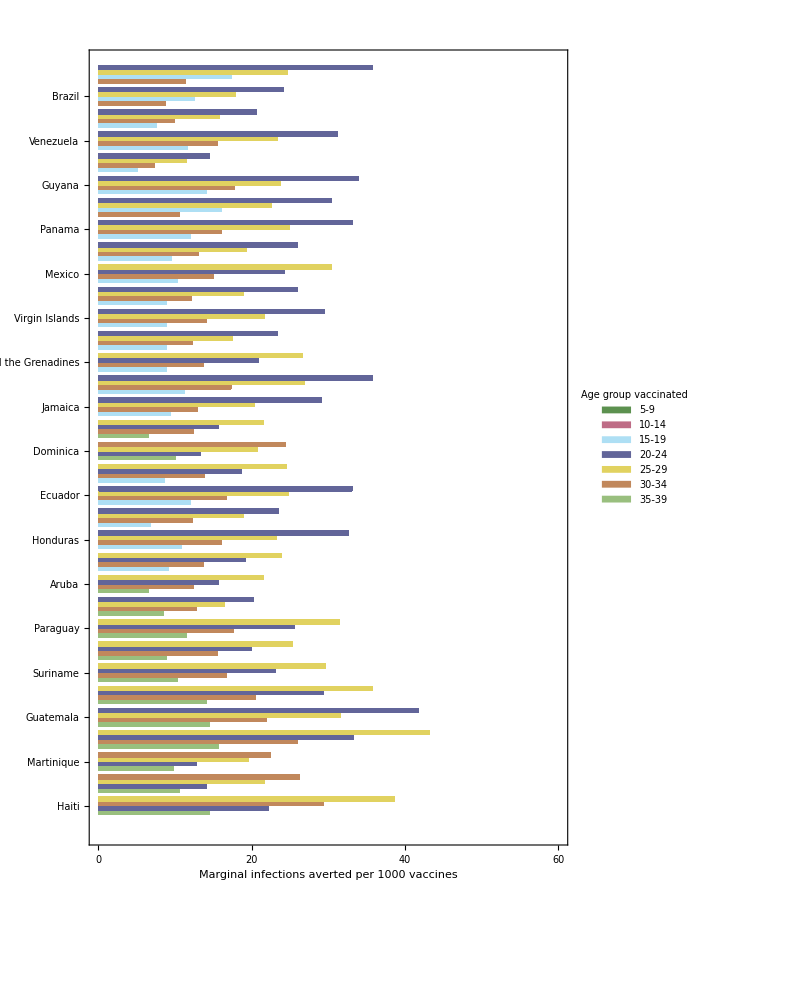

```mathematica
With[{labelsize=16,countryOrder=countryOrderMeanFertility},BarChart[Table[Style[#[[2]],stylefunc[MinMax[#[[1]]]]]&/@testdata,{testdata,(Reverse[extractExclusiveAgeGroups[#,0]]&/@countryOrder)}],
BarOrigin->Left,
BarSpacing->{0,1},
Frame->{True,True,False,False},
FrameLabel->{"","Marginal infections averted
per 1000 vaccines"},
FrameTicks->{{#,If[Mod[#,20]==0,#,""]}&/@Range[0,100,5],Automatic},
PlotRange->{0,60},

ChartLabels->{countryOrder,None},
LabelStyle->Directive[Black,labelsize],

ChartLegends->SwatchLegend[(stylefunc[#]&/@ageRange),((ToString[#[[1]]]<>"-"<>ToString[#[[2]]])&/@(ageRange)),LegendLabel->Style["Age group
vaccinated",labelsize]],

ImageSize->{600,1000},
AspectRatio->Full
]]
```

```mathematica
ageRange=Reverse[SortBy[MinMax[#]&/@DeleteDuplicates[Flatten[Table[extractExclusiveAgeGroups[country,lag][[;;4]],{country,CountryNames},{lag,{0,10}}],2][[All,1]]],First]]
```

{{35,39},{30,34},{25,29},{20,24},{15,19},{10,14},{5,9}}

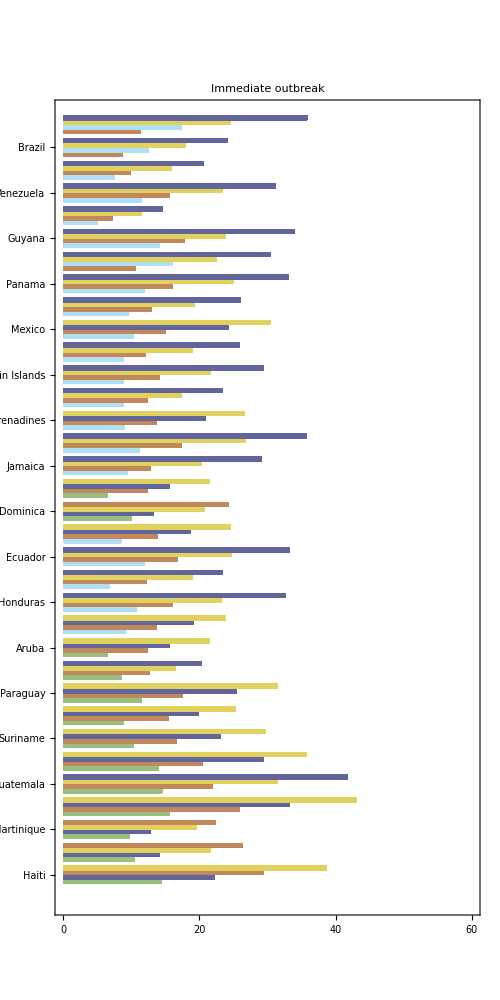
-Graphics-Marginal infections averted per 1000 vaccines

```mathematica
With[{labelsize=16,countryOrder=countryOrderMeanFertility},
Labeled[GraphicsRow[{

BarChart[Table[Style[#[[2]],stylefunc[MinMax[#[[1]]]]]&/@testdata,{testdata,(Reverse[extractExclusiveAgeGroups[#,0]]&/@countryOrder)}],
BarOrigin->Left,
BarSpacing->{0,1},
Frame->{True,True,False,False},
FrameLabel->{None,None},
FrameTicks->{{#,If[Mod[#,20]==0,#,""]}&/@Range[0,100,5],Automatic},
PlotRange->{0,60},

ChartLabels->{countryOrder,None},
LabelStyle->Directive[Black,labelsize],

PlotLabel->"Immediate outbreak",

ImageSize->{500,1000},
AspectRatio->Full
],

BarChart[Table[Style[#[[2]],stylefunc[MinMax[#[[1]]]]]&/@testdata,{testdata,(Reverse[extractExclusiveAgeGroups[#,10]]&/@countryOrder)}],
BarOrigin->Left,
BarSpacing->{0,1},
Frame->{True,True,False,False},
FrameLabel->{None,None},
FrameTicks->{{#,If[Mod[#,20]==0,#,""]}&/@Range[0,100,5],None},
PlotRange->{0,40},

ChartLabels->{None,None},
LabelStyle->Directive[Black,labelsize],

ChartLegends->SwatchLegend[(stylefunc[#]&/@ageRange),((ToString[#[[1]]]<>"-"<>ToString[#[[2]]])&/@(ageRange)),LegendLabel->Style["Age group
vaccinated",labelsize]],

PlotLabel->"Ten years until outbreak",

ImageSize->{200,1000},
AspectRatio->Full
]},0],Text[Style["Marginal infections averted per 1000 vaccines",Directive[Black,Bold,labelsize]]],Bottom]]
```

#### Report the age ranges

20-29 ages

```mathematica
Select[({#,MinMax[Flatten[extractExclusiveAgeGroups[#,0][[;;2,1]]]]}&/@CountryNames),#[[2]]=={20,29}&]
```

{{Aruba,{20,29}},{Barbados,{20,29}},{Belize,{20,29}},{Bolivia,{20,29}},{Bonaire,{20,29}},{Brazil,{20,29}},{Colombia,{20,29}},{Costa Rica,{20,29}},{Cuba,{20,29}},{Curacao,{20,29}},{Dominican Republic,{20,29}},{Ecuador,{20,29}},{El Salvador,{20,29}},{French Guiana,{20,29}},{Guatemala,{20,29}},{Guyana,{20,29}},{Honduras,{20,29}},{Jamaica,{20,29}},{Mexico,{20,29}},{Nicaragua,{20,29}},{Panama,{20,29}},{Paraguay,{20,29}},{Puerto Rico,{20,29}},{Saint Lucia,{20,29}},{Saint Martin,{20,29}},{Saint Vincent and the Grenadines,{20,29}},{Suriname,{20,29}},{Trinidad and Tobago,{20,29}},{Venezuela,{20,29}},{Virgin Islands,{20,29}}}

```mathematica
Length[Select[({#,MinMax[Flatten[extractExclusiveAgeGroups[#,0][[;;2,1]]]]}&/@CountryNames),#[[2]]=={20,29}&]]
```

30

30-34 ages

```mathematica
Select[({#,MinMax[Flatten[extractExclusiveAgeGroups[#,0][[;;2,1]]]]}&/@CountryNames),#[[2]]=={25,34}&][[All,1]]
```

{Dominica,Guadeloupe,Haiti,Martinique}

```mathematica
Length[Select[({#,MinMax[Flatten[extractExclusiveAgeGroups[#,0][[;;2,1]]]]}&/@CountryNames),#[[2]]=={25,34}&]]
```

4

#### Compute ratio of marginal benefit

Between first and second age groups

```mathematica
({#,(1-extractExclusiveAgeGroups[#,0][[2,2]]/extractExclusiveAgeGroups[#,0][[1,2]])}&/@CountryNames)//MatrixForm
```

(Aruba | 0.270218
Barbados | 0.189661
Belize | 0.248636
Bolivia | 0.178804
Bonaire | 0.270218
Brazil | 0.255155
Colombia | 0.269413
Costa Rica | 0.255096
Cuba | 0.230048
Curacao | 0.211884
Dominica | 0.145614
Dominican Republic | 0.312623
Ecuador | 0.252883
El Salvador | 0.257171
French Guiana | 0.228473
Guadeloupe | 0.176844
Guatemala | 0.244373
Guyana | 0.299515
Haiti | 0.240052
Honduras | 0.28625
Jamaica | 0.301101
Martinique | 0.123536
Mexico | 0.200247
Nicaragua | 0.257595
Panama | 0.246363
Paraguay | 0.188285
Puerto Rico | 0.206812
Saint Lucia | 0.197716
Saint Martin | 0.240879
Saint Vincent and the Grenadines | 0.218582
Suriname | 0.223847
Trinidad and Tobago | 0.191367
Venezuela | 0.250392
Virgin Islands | 0.265397)

```mathematica
Through[{MinimalBy[#,Last]&,MaximalBy[#,Last]&}[({#,(1-extractExclusiveAgeGroups[#,0][[2,2]]/extractExclusiveAgeGroups[#,0][[1,2]])}&/@CountryNames)]]
```

{{{Martinique,0.123536}},{{Dominican Republic,0.312623}}}

Between first and third age groups

```mathematica
({#,(1-extractExclusiveAgeGroups[#,0][[3,2]]/extractExclusiveAgeGroups[#,0][[1,2]])}&/@CountryNames)//MatrixForm
```

(Aruba | 0.423427
Barbados | 0.371726
Belize | 0.514789
Bolivia | 0.427968
Bonaire | 0.423427
Brazil | 0.477536
Colombia | 0.531438
Costa Rica | 0.473501
Cuba | 0.517113
Curacao | 0.386212
Dominica | 0.452279
Dominican Republic | 0.516551
Ecuador | 0.49584
El Salvador | 0.499806
French Guiana | 0.398045
Guadeloupe | 0.462442
Guatemala | 0.473388
Guyana | 0.476791
Haiti | 0.423943
Honduras | 0.507465
Jamaica | 0.557204
Martinique | 0.428607
Mexico | 0.505176
Nicaragua | 0.472167
Panama | 0.515763
Paraguay | 0.441312
Puerto Rico | 0.499475
Saint Lucia | 0.425484
Saint Martin | 0.43585
Saint Vincent and the Grenadines | 0.487881
Suriname | 0.436992
Trinidad and Tobago | 0.475113
Venezuela | 0.501006
Virgin Islands | 0.52192)

```mathematica
Through[{MinimalBy[#,Last]&,MaximalBy[#,Last]&}[({#,(1-extractExclusiveAgeGroups[#,0][[3,2]]/extractExclusiveAgeGroups[#,0][[1,2]])}&/@CountryNames)]]
```

{{{Barbados,0.371726}},{{Jamaica,0.557204}}}

### Extract specific values

```mathematica
Clear[extractExclusiveAgeGroups]
extractExclusiveAgeGroups[country_,lag_]:=With[{data=extractCEprofileByRange[country,lag]},
Prepend[
Table[
{Complement@@data[[{i+1,i},1]],data[[i+1,2]]},{i,1,Length[data]-1}
],First[data]]]
```

```mathematica
extractExclusiveAgeGroups["Brazil",0]
```

{{{20,21,22,23,24},24.904},{{25,26,27,28,29},18.2509},{{15,16,17,18,19},12.4929},{{30,31,32,33,34},8.49695}}

```mathematica
With[{country="Puerto Rico",lag=0},computedResultsFunction[noVaccineResult[country][lag],vaccResultsFrontier[country][lag]]]
```

{{709.917,97200.,0 to 4 Women},{1385.58,196200.,0 to 9 Women},{2112.55,301500.,0 to 14 Women},{3057.93,421200.,0 to 19 Women},{4073.28,547200.,0 to 24 Women},{4744.86,666000.,0 to 29 Women},{5122.22,784800.,0 to 34 Women},{5302.36,904500.,0 to 39 Women},{5393.96,1.0206×10^6,0 to 44 Women},{5457.38,1.1358×10^6,0 to 49 Women},{723.017,99000.,5 to 9 Women},{1513.93,204300.,5 to 14 Women},{2574.95,324000.,5 to 19 Women},{3750.32,450000.,5 to 24 Women},{4544.23,568800.,5 to 29 Women},{4996.82,687600.,5 to 34 Women},{5215.14,807300.,5 to 39 Women},{5327.16,923400.,5 to 44 Women},{5405.31,1.0386×10^6,5 to 49 Women},{852.996,105300.,10 to 14 Women},{2031.38,225000.,10 to 19 Women},{3377.24,351000.,10 to 24 Women},{4306.37,469800.,10 to 29 Women},{4844.64,588600.,10 to 34 Women},{5107.38,708300.,10 to 39 Women},{5243.69,824400.,10 to 44 Women},{5339.75,939600.,10 to 49 Women},{1316.26,119700.,15 to 19 Women},{2863.59,245700.,15 to 24 Women},{3958.01,364500.,15 to 29 Women},{4606.88,483300.,15 to 34 Women},{4931.95,603000.,15 to 39 Women},{5105.55,719100.,15 to 44 Women},{5230.42,834300.,15 to 49 Women},{1849.11,126000.,20 to 24 Women},{3199.09,244800.,20 to 29 Women},{4035.68,363600.,20 to 34 Women},{4485.35,483300.,20 to 39 Women},{4746.25,599400.,20 to 44 Women},{4942.8,714600.,20 to 49 Women},{1721.48,118800.,25 to 29 Women},{2852.19,237600.,25 to 34 Women},{3521.36,357300.,25 to 39 Women},{3952.53,473400.,25 to 44 Women},{4296.35,588600.,25 to 49 Women},{1430.24,118800.,30 to 34 Women},{2328.54,238500.,30 to 39 Women},{2943.51,354600.,30 to 44 Women},{3453.66,469800.,30 to 49 Women},{1098.05,119700.,35 to 39 Women},{1871.94,235800.,35 to 44 Women},{2530.79,351000.,35 to 49 Women},{886.043,116100.,40 to 44 Women},{1651.77,231300.,40 to 49 Women},{839.124,115200.,45 to 49 Women},{1402.94,198900.,0 to 4 All},{2631.77,404100.,0 to 9 All},{3708.02,625500.,0 to 14 All},{4613.79,873900.,0 to 19 All},{5199.3,1.1259×10^6,0 to 24 All},{5467.84,1.3635×10^6,0 to 29 All},{5581.1,1.5975×10^6,0 to 34 All},{5625.63,1.8315×10^6,0 to 39 All},{5644.42,2.0529×10^6,0 to 44 All},{5654.7,2.2689×10^6,0 to 49 All},{1444.86,205200.,5 to 9 All},{2806.32,426600.,5 to 14 All},{4070.43,675000.,5 to 19 All},{4944.64,927000.,5 to 24 All},{5356.04,1.1646×10^6,5 to 29 All},{5530.82,1.3986×10^6,5 to 34 All},{5599.91,1.6326×10^6,5 to 39 All},{5629.35,1.854×10^6,5 to 44 All},{5645.49,2.07×10^6,5 to 49 All},{1624.62,221400.,10 to 14 All},{3283.71,469800.,10 to 19 All},{4549.05,721800.,10 to 24 All},{5176.76,959400.,10 to 29 All},{5449.06,1.1934×10^6,10 to 34 All},{5557.84,1.4274×10^6,10 to 39 All},{5604.65,1.6488×10^6,10 to 44 All},{5630.44,1.8648×10^6,10 to 49 All},{2098.06,248400.,15 to 19 All},{3880.93,500400.,15 to 24 All},{4847.8,738000.,15 to 29 All},{5290.75,972000.,15 to 34 All},{5474.01,1.206×10^6,15 to 39 All},{5554.85,1.4274×10^6,15 to 44 All},{5599.85,1.6434×10^6,15 to 49 All},{2527.44,252000.,20 to 24 All},{4067.77,489600.,20 to 29 All},{4864.17,723600.,20 to 34 All},{5232.59,957600.,20 to 39 All},{5408.27,1.179×10^6,20 to 44 All},{5508.78,1.395×10^6,20 to 49 All},{2380.7,237600.,25 to 29 All},{3798.8,471600.,25 to 34 All},{4575.87,705600.,25 to 39 All},{4997.04,927000.,25 to 44 All},{5250.87,1.143×10^6,25 to 49 All},{2115.87,234000.,30 to 34 All},{3426.78,468000.,30 to 39 All},{4233.29,689400.,30 to 44 All},{4759.33,905400.,30 to 49 All},{1829.12,234000.,35 to 39 All},{3065.52,455400.,35 to 44 All},{3958.54,671400.,35 to 49 All},{1589.38,221400.,40 to 44 All},{2838.98,437400.,40 to 49 All},{1518.34,216000.,45 to 49 All}}

#### Compute ratio of marginal benefit

Between first and second age groups

```mathematica
({#,(1-extractExclusiveAgeGroups[#,0][[2,2]]/extractExclusiveAgeGroups[#,0][[1,2]])}&/@CountryNames)//MatrixForm
```

(Aruba | 0.270218
Barbados | 0.189661
Belize | 0.248636
Bolivia | 0.178804
Bonaire | 0.270218
Brazil | 0.255155
Colombia | 0.269413
Costa Rica | 0.255096
Cuba | 0.230048
Curacao | 0.211884
Dominica | 0.145614
Dominican Republic | 0.312623
Ecuador | 0.252883
El Salvador | 0.257171
French Guiana | 0.228473
Guadeloupe | 0.176844
Guatemala | 0.244373
Guyana | 0.299515
Haiti | 0.240052
Honduras | 0.28625
Jamaica | 0.301101
Martinique | 0.123536
Mexico | 0.200247
Nicaragua | 0.257595
Panama | 0.246363
Paraguay | 0.188285
Puerto Rico | 0.206812
Saint Lucia | 0.197716
Saint Martin | 0.240879
Saint Vincent and the Grenadines | 0.218582
Suriname | 0.223847
Trinidad and Tobago | 0.191367
Venezuela | 0.250392
Virgin Islands | 0.265397)

```mathematica
Through[{MinimalBy[#,Last]&,MaximalBy[#,Last]&}[({#,(1-extractExclusiveAgeGroups[#,0][[2,2]]/extractExclusiveAgeGroups[#,0][[1,2]])}&/@CountryNames)]]
```

{{{Martinique,0.123536}},{{Dominican Republic,0.312623}}}

Between first and third age groups

```mathematica
({#,(1-extractExclusiveAgeGroups[#,0][[3,2]]/extractExclusiveAgeGroups[#,0][[1,2]])}&/@CountryNames)//MatrixForm
```

(Aruba | 0.423427
Barbados | 0.371726
Belize | 0.514789
Bolivia | 0.427968
Bonaire | 0.423427
Brazil | 0.477536
Colombia | 0.531438
Costa Rica | 0.473501
Cuba | 0.517113
Curacao | 0.386212
Dominica | 0.452279
Dominican Republic | 0.516551
Ecuador | 0.49584
El Salvador | 0.499806
French Guiana | 0.398045
Guadeloupe | 0.462442
Guatemala | 0.473388
Guyana | 0.476791
Haiti | 0.423943
Honduras | 0.507465
Jamaica | 0.557204
Martinique | 0.428607
Mexico | 0.505176
Nicaragua | 0.472167
Panama | 0.515763
Paraguay | 0.441312
Puerto Rico | 0.499475
Saint Lucia | 0.425484
Saint Martin | 0.43585
Saint Vincent and the Grenadines | 0.487881
Suriname | 0.436992
Trinidad and Tobago | 0.475113
Venezuela | 0.501006
Virgin Islands | 0.52192)

```mathematica
Through[{MinimalBy[#,Last]&,MaximalBy[#,Last]&}[({#,(1-extractExclusiveAgeGroups[#,0][[3,2]]/extractExclusiveAgeGroups[#,0][[1,2]])}&/@CountryNames)]]
```

{{{Barbados,0.371726}},{{Jamaica,0.557204}}}